```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
Needs["SSSiCv102`"];
```

## Algorithm that will (!) work

#### Basic plan

Create or find a graph that contains some internal logic or pattern.

Use a logical numbering system to label the vertices.

List the first few (few hundred?) edges, grouping edges by originating vertex.

Form the EDSL for as much of the edge list as we have.

Summarize the EDSL using (probably nested) I-Cats (Indexed Concatenations).

Note: reconstructing the edges list from the (expanded out) EDSL is trivial, since the position of a particular edge difference set identifies the vertex number.  For example, if {d_1, d_2,..., d_m} is the n^th element of the EDSL, the edges originating from vertex n are given by {n->n+d_1,..., n->n+d_m}. The problem is to identify the vertex or vertices referred to by parts of an EDSL in reduced (I-Cat) form.

Use Position to find all lists that are not iterators inside the EDSL. The function prepIC hides iterators inside an iterator object: {var, start, stop} → iterator[var, start, stop]. (We also ignore the outer List of the EDSL.)

For each list position found, we need a formula to regenerate the vertex referred to.

This will always be a function of the I-Cat variables, the lengths already traversed, and the partially traversed in the current I-Cat(s).

Each position listed also already gives the location of the I-Cats in which it is found.  Ex/

The list at {1,1} is inside the I-Cat at {1}. Nothing already traversed.

The list at {1,2,1,1} is inside the I-Cats at {1,2,1}, {1,2}, and {1}. {1,1} already traversed.

The list at {1,2,2} is inside the I-Cats at {1,2}, and {1}. {1,2,1} and {1,1} already traversed.

The list at {1,3,1} is inside the I-Cats at {1,3}, and {1}. {1,1} & {1,2} already traversed.

The list at {1,4} is inside the I-Cat at {1}. {1,1}, {1,2} & {1,3} already traversed.

Lengths already traversed or partially traversed are found recursively.

The length of any EDS list is 1.

The length of an I-Cat is found iteratively by replacing the concatenation by a sum, and replacing the sequence of EDS lists inside the I-Cat by the sum of the lengths of the sequence terms: €_(var⊨start)^stop[term_1,term_2,…,term_k]->∑_(var=start)^stop [sum of lengths of terms]

Note 1: Since we need traversed lengths and partially-traversed lengths, we replace the upper limit by a generic variable, ℕ, and compute the sum as a function of ℕ. Once the closed-form formula has been found, we replace ℕ→stop to find the total length of the I-Cat, and replace ℕ→var-1 to find the length partially traversed when we’re considering the current iteration of var. Finally we’ll add 1 to get the vertex number for the particular EDS being considered.

Note 2: The position coordinates tell us which I-Cats to use in this length calculation, and whether to use total or partial length in each case. E.g., For the EDS at {1,2,1,1}, use partial lengths of I-Cats at {1,2,1}, {1,2}, and {1}, and total length for {1,1} (which precedes the I-Cat at {1,2} inside the one at {1}. Similarly, for {1,4} we need total lengths of I-Cats at {1,1}, {1,2}, and {1,3} and partial length for {1}, which we’re still inside. Also, the total length at {1,2} uses the total length at {1,2,1}. (Any I-Cat length formulas use the total lengths of the terms inside the I-Cat.)

Algorithm:

Function for generic, full, and partial lengths, assuming ic is already prepped using prepIC :

Take the Position information (pos) for the EDS list, add the partial length. (First time it’s guaranteed to be 1, since this is a list at this position, and by definition the length (number of vertices referred to) is 1.)

While Last[pos] > 1, decrement that last integer and add the full length of the new pos to our vertex formula.

Otherwise remove the final 1 from pos, and repeat until pos == {}.

Replace the EDS at the original pos by addV2EDS[vertex formula, EDS].

Repeat for all positions.

#### Newest code: prepIC, GLength, partialLength, fullLength, vertexFormula, addV2EDS, addVs2EDSL

Prep/UnPrep a list with I-Cats: change IndexedConcatenate to ic, make iterator objects out of iterator lists.

Consider fixing prepIC to add indexes to non indexed I-Cats!

```mathematica
prepIC[x_]:=Replace[x,IndexedConcatenate[y___,iter_List]:>ic[y,iterator[Sequence@@Flatten[{iter}]]],All];
unprepIC[x_]:=Replace[x,ic[y___,iterator[var_,start_,stop_]]:>IndexedConcatenate[y,{var,start,stop}],All];
```

```mathematica
(* these expect prepped form expressions *)
Clear[partialLength,fullLength,GLength];
partialLength[ic_] := (#[[3]] /. ℕ->#[[2]])&[GLength[ic]];
fullLength[ic_] := (#[[3]] /. ℕ->#[[1]])&[GLength[ic]];
(* replace the generic stop (ℕ) by either the original stop value or the original "i-1" *)

GLength[l_List] :=
If[
FreeQ[l,List,{2,∞}],
{ℕ,ℕ,1}, (* stop, i-1, generic length formula (no replacements done) *)
{ℕ,ℕ,Simplify[Plus @@ (fullLength /@ l)]} (* if a list of lists, add up fullLengths, no replacements *)
];

GLength[myIC_ic] := GLength[myIC]=Module[{argList,iter,var},
iter=List@@Last[myIC];
argList=Most[List@@myIC];
If[$debug,Print["myIC: ",myIC]];
If[$debug,Print["iter: ",iter]];
If[$debug,Print["argList: ",argList]];
{
iter[[3]],
iter[[1]]-1,
Factor@Sum[ (* do generic iterated Sum on full lengths of terms in the I-Cat *)
fullLength[argList] /. iter[[1]]->var,
{var,iter[[2]],ℕ} (* using local variable, orig. start, generic stop *)
]
}
];
```

```mathematica
vertexFormula[l_,pos0_List] := Module[{pos=pos0,ans=0},
While[Length[pos]>0,
ans += partialLength[Extract[l,pos]];
pos[[-1]]--;
While[Last[pos]>0,
ans += fullLength[Extract[l,pos]];
pos[[-1]]--
];
pos=Most[pos]
];
ans];
```

```mathematica
(*
addV2EDS[v_,eds_List]:= Sequence@@(Rule[v,v+#]& /@ eds);
*)
(* addV2EDSck[v_,eds_List]:= v *)

Clear[addV2EDS];
addV2EDS[v_,eds_List]:= Sequence@@(addV2EDS[v,#]&/@ eds); (* Thread, but as Sequence *)
addV2EDS[v_,ic[l___,i_iterator]] := ic[addV2EDS[v,l],i];
addV2EDS[v_,x_] := Rule[v,v+x]
```

```mathematica
addVs2EDSL[l0_]:=Module[{l,posList,eds},
l=prepIC[l0];
posList=Most/@ Rest[Position[l,List]];
If[$debug,Print["posList: ",posList]];
unprepIC@ReplacePart[l,(#->addV2EDS[vertexFormula[l,#],eds=Extract[l,#]])& /@ posList] 
];
```

```mathematica
addV2EDS[7(n-1)+2+1,{ic[2,iterator[2]]}]
```

Sequence[ic[3+7 (-1+n)→5+7 (-1+n),iterator[2]]]

```mathematica
addV2EDS[7(n-1)+3+2(i-1)+1,{1,ic[3,iterator[3]]}]
```

Sequence[4+2 (-1+i)+7 (-1+n)→5+2 (-1+i)+7 (-1+n),ic[4+2 (-1+i)+7 (-1+n)→7+2 (-1+i)+7 (-1+n),iterator[3]]]

## Try it on ICN Paper Examples

### Figure 5a

```mathematica
IC2a={IndexedConcatenate[{1},10]}
```

{€^10[{1}]}

```mathematica
IC2ap={IndexedConcatenate[{1},{i,1,10}]}
```

{€_(i⊨1)^10[{1}]}

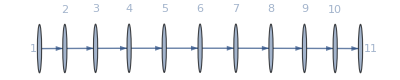

```mathematica
Graph[FromNetDifferenceSets[ExpandAll[%]],VertexLabels->Automatic,GraphLayout->"SpringElectricalEmbedding"]
```

```mathematica
{{Vertex #, , , (i-1)+1, , }, {position, , 1, 1,1, , }, {I-Cat, {, €_(i⊨1)^10[, {1}, ], }}, {reps(len), , ∑_(i=1)^ℕ (1)=ℕ, , , }, {, , , 1, ↖, }}
```

```mathematica
$debug=False;
```

```mathematica
addVs2EDSL[IC2ap]
```

{€_(i⊨1)^10[i→i+1]}

```mathematica
Graph[ExpandAll[%],VertexLabels->Automatic,GraphLayout->"SpringElectricalEmbedding"]
```

-Graphics-

### Figure 5b

```mathematica
IC2b={IndexedConcatenate[{1},{},{n,1,5}]}
```

{€_(n⊨1)^5[{1},{}]}

```mathematica
{{vertex, , , 2(n-1)
+0+1, 2(n-1)
+1+1, , }, {position, , 1, 1,1, 1,1, , }, {I-Cat, {, €_(n⊨1)^5[, {1},, {}, ], }}, {pos:∑_?^reps (len), , 1:∑_(n=1)^ℕ (1+1)
=2ℕ, , , , }, {, , , 1, 1, ↖, }}
```

```mathematica
Most /@ Rest@Position[prepIC[IC2b],List]
```

{{1,1},{1,2}}

```mathematica
addVs2EDSL[IC2b]
```

{€_(n⊨1)^5[2 (n-1)+1→2 (n-1)+2]}

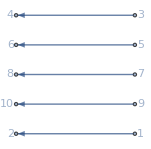

```mathematica
Graph[ExpandAll[%],VertexLabels->Automatic,GraphLayout->"SpringElectricalEmbedding"]
```

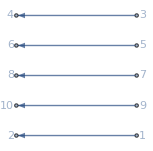

```mathematica
Graph[FromNetDifferenceSets[ExpandAll[IC2b]],VertexLabels->Automatic,GraphLayout->"SpringElectricalEmbedding"]
```

### Figure 5c

```mathematica
IC2c={IndexedConcatenate[{1,2},{n,1,10}]}
```

{€_(n⊨1)^10[{1,2}]}

```mathematica
Most /@ Rest@Position[prepIC[IC2c],List]
```

{{1,1}}

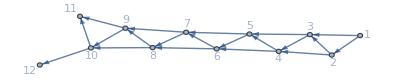

```mathematica
Graph[FromNetDifferenceSets[ExpandAll[%]],VertexLabels->Automatic,GraphLayout->"SpringElectricalEmbedding"]
```

```mathematica
{{vertex, , , 1(n-1)+1, , }, {position, , 1, 1,1, , }, {I-Cat, {, €_(n⊨1)^10[, {1,2}, ], }}, {pos:∑_?^reps (len), , 1:∑_(n=1)^10 (1)
=ℕ, , , }, {, , , 1:1, ↖, }}
```

```mathematica
addVs2EDSL[IC2c]
```

{€_(n⊨1)^10[n→n+1,n→n+2]}

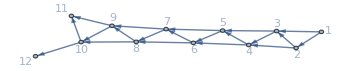

```mathematica
Graph[ExpandAll[%],VertexLabels->Automatic,GraphLayout->"SpringElectricalEmbedding"]
```

### Figure 6d

```mathematica
IC2d={IndexedConcatenate[{2,3},{3},{1,2},{m,1,9}]}
```

{€_(m⊨1)^9[{2,3},{3},{1,2}]}

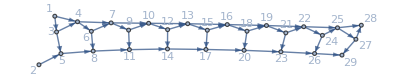

```mathematica
Graph[FromNetDifferenceSets[ExpandAll[%]],VertexLabels->Automatic,GraphLayout->"SpringElectricalEmbedding"]
```

```mathematica
{{vertex, , , 3(m-1)
+0+1, 3(m-1)
+1+1, 3(m-1) 
+2+1, , }, {position, , 1, 1,1, 1,2, 1,3, , }, {I-Cat, {, €_(m⊨1)^9[, {2,3},, {3},, {1,2}, ], }}, {pos:∑_?^reps (len), , 1:∑_(m=1)^ℕ ( 1+1+1)=3ℕ, , , , , }, {, , , 1, 1, 1, ↖, }}
```

```mathematica
Most /@ Rest@Position[prepIC[IC2d],List]
```

{{1,1},{1,2},{1,3}}

```mathematica
addVs2EDSL[IC2d]
```

{€_(m⊨1)^9[3 (m-1)+1→3 (m-1)+3,3 (m-1)+1→3 (m-1)+4,3 (m-1)+2→3 (m-1)+5,3 (m-1)+3→3 (m-1)+4,3 (m-1)+3→3 (m-1)+5]}

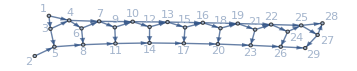

```mathematica
Graph[ExpandAll[%],VertexLabels->Automatic,GraphLayout->"SpringElectricalEmbedding"]
```

### Figure 5e

Note: This EDSL has an empty set as the sole argument of an I-Cat object, which required an adjustment to DisplayForm[IndexedConcatenate[...]] and Expand[IndexedConcatenate[...]], allowing empty arguments (before the iterator).

EDSL representations:

```mathematica
ICNB11={IndexedConcatenate[IndexedConcatenate[{2j-1, 2j}, {j, 1, 3}], IndexedConcatenate[{1, 2}, IndexedConcatenate[{},{k,1, 2}],{j,1, 2}], {i,1,3}]}
ExpandAll[ICNB11]
```

{€_(i⊨1)^3[€_(j⊨1)^3[{-1+2 j,2 j}],€_(j⊨1)^2[{1,2},€_(k⊨1)^2[{}]]]}

{{1,2},{3,4},{5,6},{1,2},{},{},{1,2},{},{},{1,2},{3,4},{5,6},{1,2},{},{},{1,2},{},{},{1,2},{3,4},{5,6},{1,2},{},{},{1,2},{},{}}

```mathematica
{{Vertex #, , , , 12(i-1)
+(j-1)
+1, , , 12(i-1)
+3
+3(j-1)
+1, , 12(i-1)
+3+3(j-1)
+1 +(k-1)
+1, , , , }, {position, , 1, 1,1, 1,1,1, , 1,2, 1,2,1, 1,2,2, 1,2,2,1, , , , }, {I-Cat, {, €_(i⊨1)^3[, €_(j⊨1)^3[, {2 j-1,2 j}, ],, €_(j⊨1)^2[, {1,2},, €_(k⊨1)^2[, {}, ], ], ], }}, {∑_?^reps (len), , ∑_(i=1)^ℕ ( 3+9)
=12ℕ, , , , , , , , , , , }, {, , , ∑_(j=1)^ℕ (1)
=ℕ=3, , , ∑_(j=1)^ℕ (1+2)
=3ℕ=9, , , , , , ↖, }, {, , , , 1, ↖, , 1, ∑_(k=1)^ℕ 1
=ℕ=2, , , ↖, , }, {, , , , , , , , , 1, ↖, , , }}
```

```mathematica
ICNB11
```

{€_(i⊨1)^3[€_(j⊨1)^3[{2 j-1,2 j}],€_(j⊨1)^2[{1,2},€_(k⊨1)^2[{}]]]}

```mathematica
addVs2EDSL[ICNB11]
```

{€_(i⊨1)^3[€_(j⊨1)^3[9 (-1+i)+j→-1+9 (-1+i)+3 j,9 (-1+i)+j→9 (-1+i)+3 j],€_(j⊨1)^2[4+9 (-1+i)+3 (-1+j)→5+9 (-1+i)+3 (-1+j),4+9 (-1+i)+3 (-1+j)→6+9 (-1+i)+3 (-1+j),€_(k⊨1)^2[]]]}

```mathematica
$debug=True;
```

```mathematica
GLength@{{1},{}}
```

{ℕ,ℕ,2}

```mathematica
GLength@{{1},{},{2}}
```

{ℕ,ℕ,3}

```mathematica
GLength@{{},{2}}
```

{ℕ,ℕ,2}

```mathematica
GLength@{{}}
```

{ℕ,ℕ,1}

```mathematica
GLength@prepIC@{IndexedConcatenate[{1},{},{2},{k,1, 2}]}
```

myIC: ic[{1},{},{2},iterator[k,1,2]]

iter: {k,1,2}

argList: {{1},{},{2}}

{ℕ,ℕ,6}

```mathematica
GLength@prepIC@{IndexedConcatenate[{1},{},{k,1, 2}]}
```

myIC: ic[{1},{},iterator[k,1,2]]

iter: {k,1,2}

argList: {{1},{}}

{ℕ,ℕ,4}

```mathematica
GLength@prepIC@{IndexedConcatenate[{},{k,1, 2}]}
```

{ℕ,ℕ,2}

```mathematica
GLength@prepIC@ICNB11
```

{ℕ,ℕ,27}

```mathematica
prepIC@ICNB11//FullForm
```

List[ic[ic[List[Plus[-1,Times[2,j]],Times[2,j]],iterator[j,1,3]],ic[List[1,2],ic[List[],iterator[k,1,2]],iterator[j,1,2]],iterator[i,1,3]]]

```mathematica
addVs2EDSL[ICNB11]
```

{€_(i⊨1)^3[€_(j⊨1)^3[9 (-1+i)+j→-1+9 (-1+i)+3 j,9 (-1+i)+j→9 (-1+i)+3 j],€_(j⊨1)^2[4+9 (-1+i)+3 (-1+j)→5+9 (-1+i)+3 (-1+j),4+9 (-1+i)+3 (-1+j)→6+9 (-1+i)+3 (-1+j),€_(k⊨1)^2[]]]}

```mathematica
ExpandAll[%]
```

{1→2,1→3,2→5,2→6,3→8,3→9,4→5,4→6,7→8,7→9,10→11,10→12,11→14,11→15,12→17,12→18,13→14,13→15,16→17,16→18,19→20,19→21,20→23,20→24,21→26,21→27,22→23,22→24,25→26,25→27}

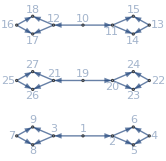

```mathematica
Graph[ExpandAll[%],VertexLabels->Automatic,GraphLayout->"SpringElectricalEmbedding"]
```

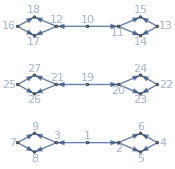

```mathematica
Graph[FromNetDifferenceSets[ExpandAll[ICNB11]],VertexLabels->Automatic,GraphLayout->"SpringElectricalEmbedding"]
```

### Figure 5f

```mathematica
ICNB2={IndexedConcatenate[{2,2,2},{1,3,3},{2},{1,1,3},{2},{1,1,1},{3},{i,1,4}]}
```

{€_(i⊨1)^4[{2,2,2},{1,3,3},{2},{1,1,3},{2},{1,1,1},{3}]}

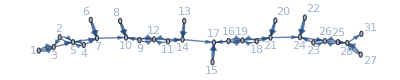

```mathematica
Graph[FromNetDifferenceSets[ExpandAll[%]],VertexLabels->Automatic,GraphLayout->"SpringElectricalEmbedding"]
```

```mathematica
{{Vertex #, , , 7(n-1)+1, 7(n-1)+2, 7(n-1)+3, 7(n-1)+4, 7(n-1)+5, 7(n-1)+6, 7(n-1)+7, , }, {position, , 1, 1,1, 1,2, 1,3, 1,4, 1,5, 1,6, 1,7, , }, {I-Cat, {, €_(n⊨1)^4[, {2,2,2},, {1,3,3},, {2},, {1,1,3},, {2},, {1,1,1},, {3}, ], }}, {pos:∑_?^reps (len), , ∑_(n=1)^4 ( 7)=7ℕ, , , , , , , , , }, {, , , 1, 1, 1, 1, 1, 1, 1, ↖, }}
```

```mathematica
addVs2EDSL[ICNB2]
```

{€_(i⊨1)^4[1+7 (-1+i)→3+7 (-1+i),1+7 (-1+i)→3+7 (-1+i),1+7 (-1+i)→3+7 (-1+i),2+7 (-1+i)→3+7 (-1+i),2+7 (-1+i)→5+7 (-1+i),2+7 (-1+i)→5+7 (-1+i),3+7 (-1+i)→5+7 (-1+i),4+7 (-1+i)→5+7 (-1+i),4+7 (-1+i)→5+7 (-1+i),4+7 (-1+i)→7+7 (-1+i),5+7 (-1+i)→7+7 (-1+i),6+7 (-1+i)→7+7 (-1+i),6+7 (-1+i)→7+7 (-1+i),6+7 (-1+i)→7+7 (-1+i),7+7 (-1+i)→10+7 (-1+i)]}

```mathematica
Graph[ExpandAll[%],VertexLabels->Automatic,GraphLayout->"SpringElectricalEmbedding"]
```

-Graphics-

### Figure 5g

```mathematica
ICNB3={IndexedConcatenate[{2, 3}, {1, 2}, {}, {i,1,8}]}
```

{€_(i⊨1)^8[{2,3},{1,2},{}]}

```mathematica
Most /@ Rest[Position[prepIC[ICNB3],List]]
```

{{1,1},{1,2},{1,3}}

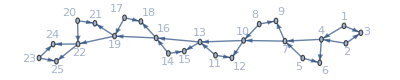

```mathematica
Graph[FromNetDifferenceSets[ExpandAll[%]],VertexLabels->Automatic,GraphLayout->"SpringElectricalEmbedding"]
```

```mathematica
{{Vertex #, , , 3(n-1)+1, 3(n-1)+2, 3(n-1)+3, , }, {position, , 1, 1,1, 1,2, 1,3, , }, {I-Cat, {, €_(n⊨1)^8[, {2,3}, {1,2}, {}, ], }}, {∑_?^reps (len), , ∑_(n=1)^8 ( 3)=3ℕ, , , , , }, {, , , 1, 1, 1, ↖, }}
```

```mathematica
addVs2EDSL[ICNB3]
```

{€_(i⊨1)^8[1+3 (-1+i)→3+3 (-1+i),1+3 (-1+i)→4+3 (-1+i),2+3 (-1+i)→3+3 (-1+i),2+3 (-1+i)→4+3 (-1+i)]}

```mathematica
Graph[ExpandAll[%],VertexLabels->Automatic,GraphLayout->"SpringElectricalEmbedding"]
```

-Graphics-

### Figure 5h

```mathematica
ICNB4={IndexedConcatenate[{1, 6, 8}, {}, {IndexedConcatenate[2,4]}, IndexedConcatenate[{1, IndexedConcatenate[3,3]}, {}, 2], 7]}
```

{€^7[{1,6,8},{},{€^4[2]},€^2[{1,€^3[3]},{}]]}

```mathematica
ICNB4a={IndexedConcatenate[{1, 6, 8}, {}, {IndexedConcatenate[2,{j,1,4}]}, IndexedConcatenate[{1, IndexedConcatenate[3,{k,1,3}]}, {}, {j,1,2}], {i,1,7}]}
```

{€_(i⊨1)^7[{1,6,8},{},{€_(j⊨1)^4[2]},€_(j⊨1)^2[{1,€_(k⊨1)^3[3]},{}]]}

```mathematica
Most /@ Rest[Position[prepIC[ICNB4],List]]
```

{{1,1},{1,2},{1,3},{1,4,1},{1,4,2}}

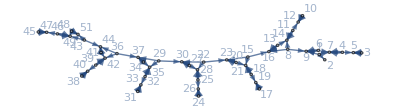

```mathematica
Graph[FromNetDifferenceSets[ExpandAll[ICNB4]],VertexLabels->Automatic,GraphLayout->"SpringElectricalEmbedding"]
```

```mathematica
{{Vertex #, , , 7(n-1)
+1, 7(n-1)
+1+1, 7(n-1)
+2+1, , 7(n-1)
+3+2(i-1)
+1, 7(n-1)
+3+2(i-1)
+1+1, , , }, {position, , 1, 1,1, 1,2, 1,3, 1,4, 1,4,1, 1,4,2, , , }, {I-Cat, {, €_(n⊨1)^7, {1,6,8},, {},, {€_(i⊨1)^4[2]}, €_(j⊨1)^2[, {1,€^3[3]},, {}, ], ], }}, {pos:∑_?^reps (len), , 1:∑_(n=1)^ℕ (1+1+1+4)=7ℕ, , , , , , , , , }, {, , , 1, 1, 1, ∑_(j=1)^ℕ 2=2ℕ=4, , , , ↖, }, {, , , , , , , 1, 1, ↖, , }}
```

Note the I-Cat objects remaining in {1,3} and {1,4,1} !! Vertex # is not affected, but the number of edges is. Treat either by pre-expanding or by nesting the edge description inside these I-Cats.

```mathematica
addVs2EDSL[ICNB4a]
```

{€_(i⊨1)^7[1+7 (-1+i)→2+7 (-1+i),1+7 (-1+i)→7+7 (-1+i),1+7 (-1+i)→9+7 (-1+i),€_(j⊨1)^4[3+7 (-1+i)→5+7 (-1+i)],€_(j⊨1)^2[4+7 (-1+i)+2 (-1+j)→5+7 (-1+i)+2 (-1+j),€_(k⊨1)^3[4+7 (-1+i)+2 (-1+j)→7+7 (-1+i)+2 (-1+j)]]]}

```mathematica
Graph[ExpandAll[%],VertexLabels->Automatic,GraphLayout->"SpringElectricalEmbedding"]
```

-Graphics-

Now vertex information can be added correctly when the EDS contains an I-Cat!

### Figure 5i

```mathematica
ICB5={IndexedConcatenate[IndexedConcatenate[{1,18-2k},{k,1,7}],IndexedConcatenate[{1,1},{k,8,9}],{n,0,25}]}
```

{€_(n⊨0)^25[€_(k⊨1)^7[{1,18-2 k}],€_(k⊨8)^9[{1,1}]]}

```mathematica
Most /@ Rest[Position[prepIC[ICB5],List]]
```

{{1,1,1},{1,2,1}}

```mathematica
Graph[FromNetDifferenceSets[ExpandAll[%]],VertexLabels->None,GraphLayout->"SpringElectricalEmbedding"]
```

-Graphics-

```mathematica
{{Vertex #, , , , 9((n-1)+1) 
+(k-1)
+1, , , 9((n-1)+1) 
+7+(k-1-7)
+1, , , }, {position, , 1, 1,1, 1,1,1, , 1,2, 1,2,1, , , }, {I-Cat, {, €_(n⊨0)^25[, €_(k⊨1)^7[, {1,18-2k}, ],, €_(k⊨8)^9[, {1,1}, ], ], }}, {pos:∑_?^reps (len), , 1:∑_(n=0)^ℕ ( 9)=9(ℕ+1), , , , , , , , }, {, , , ∑_(k=1)^ℕ (1)=ℕ=7, , , ∑_(k=8)^ℕ (1)=(ℕ-7)=2, , , ↖, }, {, , , , 1, ↖, , 1, ↖, , }}
```

```mathematica
addVs2EDSL[ICB5]
```

{€_(n⊨0)^25[€_(k⊨1)^7[k+9 n→1+k+9 n,k+9 n→18-k+9 n],€_(k⊨8)^9[k+9 n→1+k+9 n,k+9 n→1+k+9 n]]}

```mathematica
Graph[ExpandAll[%],VertexLabels->None,GraphLayout->"SpringElectricalEmbedding"]
```

-Graphics-

### Figure 5j

```mathematica
ICB6={IndexedConcatenate[IndexedConcatenate[{1,7,8},2],IndexedConcatenate[{1,1,7},2],{7},{},{},13]}
```

{€^13[€^2[{1,7,8}],€^2[{1,1,7}],{7},{},{}]}

```mathematica
ICB6p={IndexedConcatenate[IndexedConcatenate[{1,7,8},{j,1,2}],IndexedConcatenate[{1,1,7},{j,1,2}],{7},{},{},{n,1,13}]}
```

{€_(n⊨1)^13[€_(j⊨1)^2[{1,7,8}],€_(j⊨1)^2[{1,1,7}],{7},{},{}]}

```mathematica
Most /@ Rest[Position[prepIC[ICB6p],List]]
```

{{1,1,1},{1,2,1},{1,3},{1,4},{1,5}}

```mathematica
{{Vertex #, , , , 7(n-1)
+(j-1)
+1, , , 7(n-1)
+2+(j-1)
+1, , 7(n-1)
+4
+1, 7(n-1)
+5
+1, 7(n-1)
+6
+1, , }, {position, , 1, 1,1, 1,1,1, , 1,2, 1,2,1, , 1,3, 1,4, 1,5, , }, {I-Cat, {, €_(i⊨1)^13[, €_(j⊨1)^2[, {1,7,8}, ],, €_(j⊨1)^2[, {1,1,7}, ],, {7},, {},, {}, ], }}, {pos:∑_?^reps (len), , ∑_(n=1)^ℕ ( 7)=7ℕ, , , , , , , , , , , }, {, , , ∑_(j=1)^ℕ (1)=ℕ=2, , , ∑_(j=1)^ℕ (1)=ℕ=2, , , 1, 1, 1, ↖, }, {, , , , 1, ↖, , 1, ↖, , , , , }}
```

```mathematica
addVs2EDSL[ICB6p]
```

{€_(n⊨1)^13[€_(j⊨1)^2[j+7 (n-1)→j+7 (n-1)+1,j+7 (n-1)→j+7 (n-1)+7,j+7 (n-1)→j+7 (n-1)+8],€_(j⊨1)^2[j+7 (n-1)+2→j+7 (n-1)+3,j+7 (n-1)+2→j+7 (n-1)+3,j+7 (n-1)+2→j+7 (n-1)+9],7 (n-1)+5→7 (n-1)+12]}

```mathematica
Graph[ExpandAll[%],VertexLabels->None,GraphLayout->"SpringElectricalEmbedding"]
```

-Graphics-

```mathematica
Graph[FromNetDifferenceSets@ExpandAll[ICB6],VertexLabels->None,GraphLayout->"SpringElectricalEmbedding"]
```

-Graphics-

### Figure 5k

```mathematica
ICB5b={IndexedConcatenate[IndexedConcatenate[{1,12-2k},{k,1,4}],IndexedConcatenate[{1,1},{k,5,7}],{n,0,18}]}
```

{€_(n⊨0)^18[€_(k⊨1)^4[{1,12-2 k}],€_(k⊨5)^7[{1,1}]]}

```mathematica
Most /@ Rest[Position[prepIC[ICB5b],List]]
```

{{1,1,1},{1,2,1}}

```mathematica
{{Vertex #, , , , 7n
+(k-1)
+1, , , 7n
+4+((k-1)-4)
+1, , , }, {position, , 1, 1,1, 1,1,1, , 1,2, 1,2,1, , , }, {I-Cat, {, €_(n⊨0)^18, €_(k⊨1)^4[, {1,12-2 k}, ],, €_(k⊨5)^7[, {1,1}, ], ], }}, {pos:∑_?^reps (len), , ∑_(n=0)^ℕ ( 7)=7(ℕ+1), , , , , , , , }, {, , , ∑_(k=1)^ℕ (1)=ℕ=4, , , ∑_(k=5)^ℕ (1)=ℕ-4=3, , , ↖, }, {, , , , 1, ↖, , 1, ↖, , }}
```

```mathematica
addVs2EDSL[ICB5b]
```

{€_(n⊨0)^18[€_(k⊨1)^4[k+7 n→k+7 n+1,k+7 n→-k+7 n+12],€_(k⊨5)^7[k+7 n→k+7 n+1,k+7 n→k+7 n+1]]}

```mathematica
Graph[ExpandAll[%],VertexLabels->None,GraphLayout->"SpringElectricalEmbedding"]
```

-Graphics-

```mathematica
Graph[FromNetDifferenceSets[ExpandAll[ICB5b]],VertexLabels->None,GraphLayout->"SpringElectricalEmbedding"]
```

-Graphics-

### Figure 6a

```mathematica
IC2D1={IndexedConcatenate[{1,1,1},{1,1,1+i},IndexedConcatenate[{1,1,2+i},-1+i],{2+i,3+i},{i,1,10}]}
```

{€_(i⊨1)^10[{1,1,1},{1,1,1+i},€^(-1+i)[{1,1,2+i}],{2+i,3+i}]}

```mathematica
IC2D1p={IndexedConcatenate[{1,1,1},{1,1,1+i},IndexedConcatenate[{1,1,2+i},{j,1,-1+i}],{2+i,3+i},{i,1,10}]}
```

{€_(i⊨1)^10[{1,1,1},{1,1,1+i},€_(j⊨1)^(-1+i)[{1,1,2+i}],{2+i,3+i}]}

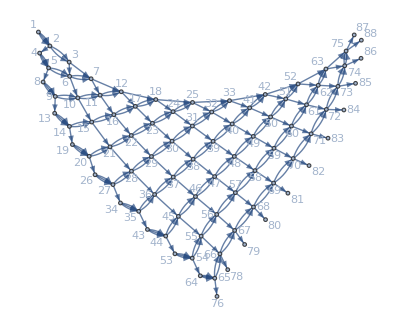

```mathematica
Graph[FromNetDifferenceSets[ExpandAll[%]],VertexLabels->Automatic,GraphLayout->"SpringElectricalEmbedding"]
```

```mathematica
Most /@ Rest@Position[prepIC[IC2D1],List]
```

{{1,1},{1,2},{1,3,1},{1,4}}

```mathematica
{{Vertex #, , , ((i-1)^2+5(i-1))/2
+0
+1, ((i-1)^2+5(i-1))/2
+1
+1, , ((i-1)^2+5(i-1))/2
+1+1
+(j-1)
+1, , ((i-1)^2+5(i-1))/2
+1+1+(i-1)
+1, , , }, {position, , 1, 1,1, 1,2, 1,3, 1,3,1, , 1,4, , , }, {I-Cat, {, €_(i⊨1)^10[, {1,1,1},, {1,1,i+1},, €_(j⊨1)^(i-1)[, {1,1,i+2}, ],, {i+2,i+3}, ], ], }}, {pos:∑_?^reps (len), , ∑_(i=1)^10 (1+1+i-1+1)
=1/2 (ℕ^2+5 ℕ), , , , , , , , , }, {, , , 1, 1, ∑_j^(i-1) (1)=ℕ=i-1, , , 1, , ↖, }, {, , , , , , 1, ↖, , , , }}
```

```mathematica
addVs2EDSL[IC2D1p]
```

{€_(i⊨1)^10[1+1/2 (-1+i) (4+i)→2+1/2 (-1+i) (4+i),1+1/2 (-1+i) (4+i)→2+1/2 (-1+i) (4+i),1+1/2 (-1+i) (4+i)→2+1/2 (-1+i) (4+i),2+1/2 (-1+i) (4+i)→3+1/2 (-1+i) (4+i),2+1/2 (-1+i) (4+i)→3+1/2 (-1+i) (4+i),2+1/2 (-1+i) (4+i)→3+i+1/2 (-1+i) (4+i),€_(j⊨1)^(-1+i)[2+1/2 (-1+i) (4+i)+j→3+1/2 (-1+i) (4+i)+j,2+1/2 (-1+i) (4+i)+j→3+1/2 (-1+i) (4+i)+j,2+1/2 (-1+i) (4+i)+j→4+i+1/2 (-1+i) (4+i)+j],2+i+1/2 (-1+i) (4+i)→4+2 i+1/2 (-1+i) (4+i),2+i+1/2 (-1+i) (4+i)→5+2 i+1/2 (-1+i) (4+i)]}

```mathematica
Graph[ExpandAll[%],VertexLabels->None,GraphLayout->"SpringElectricalEmbedding"]
```

-Graphics-

```mathematica
Graph[FromNetDifferenceSets[ExpandAll[IC2D1p]],VertexLabels->None,GraphLayout->"SpringElectricalEmbedding"]
```

-Graphics-

### Figure 6b

```mathematica
IC2D2={IndexedConcatenate[{-1+2 k,1+2 k},IndexedConcatenate[{1,1},{1,2 k},k],{k,1,12}]}
```

{€_(k⊨1)^12[{-1+2 k,1+2 k},€^k[{1,1},{1,2 k}]]}

```mathematica
IC2D2p={IndexedConcatenate[{-1+2 k,1+2 k},IndexedConcatenate[{1,1},{1,2 k},{j,1,k}],{k,1,12}]}
```

{€_(k⊨1)^12[{2 k-1,2 k+1},€_(j⊨1)^k[{1,1},{1,2 k}]]}

```mathematica
Most /@ Rest[Position[prepIC[IC2D2],List]]
```

{{1,1},{1,2,1},{1,2,2}}

```mathematica
{{Vertex #, , , (k-1) (k-1+2) 
+0+1, , (k-1) (k+1)
+1+ 2(j-1)
+1, (k-1) (k+1)
+1+ 2(j-1)
+1+1, , , }, {position, , 1, 1,1, 1,2, 1,2,1, 1,2,2, , , }, {I-Cat, {, €_(k⊨1)^12, {2k-1,2k+1},, €_(j⊨1)^k[, {1,1},, {1,2k}, ], ], }}, {pos:∑_?^reps (len), , ∑_(k=1)^ℕ ( 1+2k)=ℕ (ℕ+2), , , , , , , }, {, , , 1, ∑_(j=1)^ℕ (2)=2ℕ=2k, , , , ↖, }, {, , , , , 1, 1, ↖, , }}
```

```mathematica
addVs2EDSL[IC2D2p]
```

{€_(k⊨1)^12[(k-1) (k+1)+1→2 k+(k-1) (k+1),(k-1) (k+1)+1→2 k+(k-1) (k+1)+2,€_(j⊨1)^k[2 (j-1)+(k-1) (k+1)+2→2 (j-1)+(k-1) (k+1)+3,2 (j-1)+(k-1) (k+1)+2→2 (j-1)+(k-1) (k+1)+3,2 (j-1)+(k-1) (k+1)+3→2 (j-1)+(k-1) (k+1)+4,2 (j-1)+(k-1) (k+1)+3→2 (j-1)+2 k+(k-1) (k+1)+3]]}

```mathematica
Graph[ExpandAll[%],VertexLabels->None,GraphLayout->"SpringElectricalEmbedding"]
```

-Graphics-

```mathematica
Graph[FromNetDifferenceSets[ExpandAll[%]],VertexLabels->None,GraphLayout->"SpringElectricalEmbedding"]
```

-Graphics-

### Figure 6c

```mathematica
IC2D4={IndexedConcatenate[IndexedConcatenate[{},{1,1,2,2k},k-1],{},{2k,2(1+k)},{k,1,8}]}
```

{€_(k⊨1)^8[€^(-1+k)[{},{1,1,2,2 k}],{},{2 k,2 (1+k)}]}

```mathematica
IC2D4p={IndexedConcatenate[IndexedConcatenate[{},{1,1,2,2k},{j,1,k-1}],{},{2k,2(1+k)},{k,1,8}]}
```

{€_(k⊨1)^8[€_(j⊨1)^(k-1)[{},{1,1,2,2 k}],{},{2 k,2 (k+1)}]}

```mathematica
Most/@Rest[Position[prepIC[IC2D4],List]]
```

{{1,1,1},{1,1,2},{1,2},{1,3}}

```mathematica
{{Vertex #, , , , (k-1) k
+ 2(j-1)
+0+1, (k-1) k
+ 2(j-1)
+1+1, , (k-1)k
+2(k-1)
+1, (k-1)k
+2(k-1)+1
+1, , }, {position, , 1, 1,1, 1,1,1, 1,1,2, , 1,2, 1,3, , }, {I-Cat, {, €_(k⊨1)^8[, €_(j⊨1)^(k-1)[, {}, {1,1}, ],, {}, {2k,2k+2}, ], }}, {pos:∑_?^reps (len), , ∑_(k=1)^ℕ ( 2k)=ℕ (ℕ+1), , , , , , , , }, {, , , ∑_(j=1)^ℕ (2)=2ℕ
=2(k-1), , , , 1, 1, ↖, }, {, , , , 1, 1, ↖, , , , }}
```

```mathematica
addVs2EDSL[IC2D4p]
```

{€_(k⊨1)^8[€_(j⊨1)^(-1+k)[2+2 (-1+j)+(-1+k) k→3+2 (-1+j)+(-1+k) k,2+2 (-1+j)+(-1+k) k→3+2 (-1+j)+(-1+k) k,2+2 (-1+j)+(-1+k) k→4+2 (-1+j)+(-1+k) k,2+2 (-1+j)+(-1+k) k→2+2 (-1+j)+2 k+(-1+k) k],2+2 (-1+k)+(-1+k) k→2+2 (-1+k)+2 k+(-1+k) k,2+2 (-1+k)+(-1+k) k→2+2 (-1+k)+(-1+k) k+2 (1+k)]}

```mathematica
Graph[ExpandAll[%],VertexLabels->None,GraphLayout->"SpringElectricalEmbedding"]
```

-Graphics-

```mathematica
Graph[FromNetDifferenceSets[ExpandAll[IC2D4]],VertexLabels->None,GraphLayout->"SpringElectricalEmbedding"]
```

-Graphics-

### Figure 6d

```mathematica
IC3D1={IndexedConcatenate[IndexedConcatenate[IndexedConcatenate[{z=n(n+1)/2,z+i,z+i+1},i],{i,1,n}],{n,1,5}]}
```

{€_(n⊨1)^5[€_(i⊨1)^n[€^i[{1/2 n (1+n),i+1/2 n (1+n),1+i+1/2 n (1+n)}]]]}

```mathematica
IC3D1p={IndexedConcatenate[IndexedConcatenate[IndexedConcatenate[{z=n(n+1)/2,z+i,z+i+1},{j,1,i}],{i,1,n}],{n,1,5}]}
```

{€_(n⊨1)^5[€_(i⊨1)^n[€_(j⊨1)^i[{1/2 n (n+1),i+1/2 n (n+1),i+1/2 n (n+1)+1}]]]}

```mathematica
{{vertex, , , , , ((n-1)((n-1)+1) ((n-1)+2))/6+((i-1)((i-1)+1))/2+(j-1)+1, , , , }, {position, , 1, 1,1, 1,1,1, 1,1,1,1, , , , }, {I-Cat, {, €_(n⊨1)^5, €_(i⊨1)^n[, €_(j⊨1)^i[, {z=1/2 n (1+n),i+z,1+i+z}, ], ], ], }}, {∑_?^reps (len), , ∑_(n=1)^ℕ ( (n(n+1))/2)
=(ℕ (ℕ+1) (ℕ+2))/6, , , , , , , }, {, , , ∑_(i=1)^ℕ (i)=(ℕ(ℕ+1))/2, , , , , ↖, }, {, , , , ∑_(j=1)^ℕ ( 1)=ℕ, , , ↖, , }, {, , , , , 1, ↖, , , }}
```

```mathematica
addVs2EDSL[IC3D1p]
```

{€_(n⊨1)^5[€_(i⊨1)^n[€_(j⊨1)^i[1/2 (-1+i) i+j+1/6 (-1+n) n (1+n)→1/2 (-1+i) i+j+1/2 n (1+n)+1/6 (-1+n) n (1+n),1/2 (-1+i) i+j+1/6 (-1+n) n (1+n)→i+1/2 (-1+i) i+j+1/2 n (1+n)+1/6 (-1+n) n (1+n),1/2 (-1+i) i+j+1/6 (-1+n) n (1+n)→1+i+1/2 (-1+i) i+j+1/2 n (1+n)+1/6 (-1+n) n (1+n)]]]}

```mathematica
Graph3D[ExpandAll[%],VertexLabels->Automatic,GraphLayout->"SpringElectricalEmbedding"]
```

-Graphics3D-

```mathematica
Graph3D[FromNetDifferenceSets[ExpandAll[IC3D1p]],VertexLabels->Automatic,GraphLayout->"SpringElectricalEmbedding"]
```

-Graphics3D-

#### Musings:

The len of an I-Cat, e.g., €_(var⊨start)^stop[stuff] seems to be found by replacing the I-Cat by  ∑_(var=start)^stop len(stuff), where len is further defined recursively, with len[a list with no nested lists] = 1, while len[a sequence] is the sum of len of its elements, and len[
the vertex formula seems to have one term from each I-Cat we’re inside, based on the finite sum found by replacing €_(var⊨start)^stop[stuff] by ∑_(var=start)^N len(stuff), where len is defined recursively, with len[a list with no nested lists] = 1, while len[a sequence] is the sum of len of its elements.

Then the vertex formula for a list inside nested I-Cats has a term for each of them, where the same sum is found, but ℕ is replaced by (var - 1), or 0, whichever is larger. For example, the finite sums found above in the recursive calculation of lengths were 

(ℕ (ℕ+1) (ℕ+2))/6, (n(n+1))/2, and i. The corresponding terms in the vertex formula are

((n-1)((n-1)+1) ((n-1)+2))/6+((i-1)((i-1)+1))/2+(j-1). The final +1 in the formula may be because this list’s position was {1,1,1,1} -- ending in 1, or more likely 1 more than the sum of len applied to all previous terms (here there are none) inside these I-Cats.

Both functions can be served if the sum is found with an arbitrary stop, such as ℕ, in the outer case above, and then for len, ℕ→stop, while for the vertex formula term, ℕ→(var-start), or something similar.

### Figure 6e

```mathematica
IC2c={IndexedConcatenate[IndexedConcatenate[{k,k+1},k],{k,1,9}]}
```

{€_(k⊨1)^9[€^k[{k,1+k}]]}

```mathematica
IC2cp={IndexedConcatenate[IndexedConcatenate[{k,k+1},{j,1,k}],{k,1,9}]}
```

{€_(k⊨1)^9[€_(j⊨1)^k[{k,1+k}]]}

```mathematica
Most/@Rest[Position[prepIC[IC2c],List]]
```

{{1,1,1}}

```mathematica
{{Vertex #, , , , (k-1) k/2
+(j-1)
+0+1, , , }, {position, , 1, 1,1, 1,1,1, , , }, {I-Cat, {, €_(k⊨1)^9[, €_(j⊨1)^k[, {k,k+1}, ], ], }}, {pos:∑_?^reps (len), , ∑_(k=1)^ℕ (k)=ℕ (ℕ+1)/2, , , , , }, {, , , ∑_(j=1)^ℕ (1)=ℕ=k, , , ↖, }, {, , , , 1, ↖, , }}
```

```mathematica
addVs2EDSL[IC2cp]
```

{€_(k⊨1)^9[€_(j⊨1)^k[j+1/2 (k-1) k→j+1/2 (k-1) k+k,j+1/2 (k-1) k→j+1/2 (k-1) k+k+1]]}

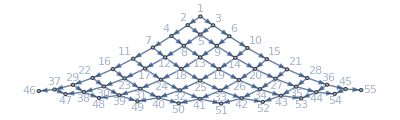

```mathematica
Graph[ExpandAll[%],VertexLabels->Automatic,GraphLayout->"SpringElectricalEmbedding"]
```

```mathematica
Graph[FromNetDifferenceSets[ExpandAll[IC2cp]],VertexLabels->Automatic,GraphLayout->"SpringElectricalEmbedding"]
```

-Graphics-

### Figure 6f

```mathematica
IC2j={IndexedConcatenate[{-1 + 2^k, 2^k, 1 + 2^k}, IndexedConcatenate[{1 + 2^k}, 1 + 2^k], {1}, 
 IndexedConcatenate[{1, -1 + 2^k + j, 2^k + j}, {j, 1, -1 + 2^k}], {k, 1, 10}]}
```

{€_(k⊨1)^10[{-1+2^k,2^k,1+2^k},€^(1+2^k)[{1+2^k}],{1},€_(j⊨1)^(-1+2^k)[{1,-1+2^k+j,2^k+j}]]}

```mathematica
IC2jp={IndexedConcatenate[{-1 + 2^k, 2^k, 1 + 2^k}, IndexedConcatenate[{1 + 2^k},{j,1, 1 + 2^k}], {1}, 
 IndexedConcatenate[{1, -1 + 2^k + j, 2^k + j}, {j, 1, -1 + 2^k}], {k, 1, 10}]}
```

{€_(k⊨1)^10[{-1+2^k,2^k,1+2^k},€_(j⊨1)^(1+2^k)[{1+2^k}],{1},€_(j⊨1)^(-1+2^k)[{1,j+2^k-1,j+2^k}]]}

```mathematica
Most/@Rest[Position[prepIC[IC2j],List]]
```

{{1,1},{1,2,1},{1,3},{1,4,1}}

```mathematica
{{Vertex #, , , 2^(k+1)+2k-6

+0+1, , 2^(k+1)+2k-6
+1+ 2(j-1)
+1, , 2^(k+1)+2k-6
+1+(2^k+1)
+1, , 2^(k+1)+2k-6
+1+(2^k+1)+1
+(j-1)
+1, , , }, {position, , 1, 1,1, 1,2, 1,2,1, , 1,3, 1,4, 1,4,1, , , }, {I-Cat, {, €_(k⊨1)^10[, {2^k-1,2^k,2^k+1},, €_(j⊨1)^(2^k+1)[, {2^k+1}, ],, {1}, €_(j⊨1)^(2^k-1), {1,2^k+j-1,2^k+j}, ], ], }}, {pos:∑_?^reps (len), , ∑_(k=1)^ℕ ( 2^(k+1)+2)
=2^(ℕ+2)+2ℕ-4, , , , , , , , , , }, {, , , 1, ∑_(j=1)^ℕ (1)=ℕ
=(2^k+1), , , 1, ∑_(j=1)^ℕ (1)=ℕ
=(2^k-1), , , ↖, }, {, , , , , 1, ↖, , , 1, ↖, , }}
```

```mathematica
addVs2EDSL[IC2jp]
```

{€_(k⊨1)^10[2 (k+2^k-3)+1→2 (k+2^k-3)+2^k,2 (k+2^k-3)+1→2 (k+2^k-3)+2^k+1,2 (k+2^k-3)+1→2 (k+2^k-3)+2^k+2,€_(j⊨1)^(1+2^k)[j+2 (k+2^k-3)+1→j+2^k+2 (k+2^k-3)+2],2 (k+2^k-3)+2^k+3→2 (k+2^k-3)+2^k+4,€_(j⊨1)^(-1+2^k)[j+2^k+2 (k+2^k-3)+3→j+2^k+2 (k+2^k-3)+4,j+2^k+2 (k+2^k-3)+3→2 j+2^(k+1)+2 (k+2^k-3)+2,j+2^k+2 (k+2^k-3)+3→2 j+2^(k+1)+2 (k+2^k-3)+3]]}

```mathematica
Graph3D[ExpandAll[%],VertexLabels->None,GraphLayout->"SpringElectricalEmbedding"]
```

-Graphics3D-

```mathematica
Graph3D[FromNetDifferenceSets[ExpandAll[IC2jp]],VertexLabels->None,GraphLayout->"SpringElectricalEmbedding"]
```

-Graphics3D-

### Nested Pentagon Example

```mathematica
pentagraph={IndexedConcatenate[
{1,5n+4,5n+5},
IndexedConcatenate[
IndexedConcatenate[{1},{i,1,n}],
{1,5n+5+k},
{k,1,4}],
IndexedConcatenate[{1},{j,1,n-1}],
{},
{n,1,8}]};
pentagraph
Graph3D[FromNetDifferenceSets[ExpandAll[pentagraph]]]
```

{€_(n⊨1)^8[{1,5 n+4,5 n+5},€_(k⊨1)^4[€_(i⊨1)^n[{1}],{1,k+5 n+5}],€_(j⊨1)^(n-1)[{1}],{}]}

-Graphics3D-

```mathematica
pentagraph//ExpandAll
```

{{1,9,10},{1},{1,11},{1},{1,12},{1},{1,13},{1},{1,14},{},{1,14,15},{1},{1},{1,16},{1},{1},{1,17},{1},{1},{1,18},{1},{1},{1,19},{1},{},{1,19,20},{1},{1},{1},{1,21},{1},{1},{1},{1,22},{1},{1},{1},{1,23},{1},{1},{1},{1,24},{1},{1},{},{1,24,25},{1},{1},{1},{1},{1,26},{1},{1},{1},{1},{1,27},{1},{1},{1},{1},{1,28},{1},{1},{1},{1},{1,29},{1},{1},{1},{},{1,29,30},{1},{1},{1},{1},{1},{1,31},{1},{1},{1},{1},{1},{1,32},{1},{1},{1},{1},{1},{1,33},{1},{1},{1},{1},{1},{1,34},{1},{1},{1},{1},{},{1,34,35},{1},{1},{1},{1},{1},{1},{1,36},{1},{1},{1},{1},{1},{1},{1,37},{1},{1},{1},{1},{1},{1},{1,38},{1},{1},{1},{1},{1},{1},{1,39},{1},{1},{1},{1},{1},{},{1,39,40},{1},{1},{1},{1},{1},{1},{1},{1,41},{1},{1},{1},{1},{1},{1},{1},{1,42},{1},{1},{1},{1},{1},{1},{1},{1,43},{1},{1},{1},{1},{1},{1},{1},{1,44},{1},{1},{1},{1},{1},{1},{},{1,44,45},{1},{1},{1},{1},{1},{1},{1},{1},{1,46},{1},{1},{1},{1},{1},{1},{1},{1},{1,47},{1},{1},{1},{1},{1},{1},{1},{1},{1,48},{1},{1},{1},{1},{1},{1},{1},{1},{1,49},{1},{1},{1},{1},{1},{1},{1},{}}

{€_(n⊨1)^8[{1,5 n+4,5 n+5},€_(k⊨1)^4[€_(i⊨1)^n[{1}],{1,k+5 n+5}],€_(j⊨1)^(n-1)[{1}],{}]}

```mathematica
{{Vertex #, , , (5(n-1)(n+2))/2
+1, , , (5(n-1)(n+2))/2
+1+(k-1)(n+1)
+(i-1)
+1, , (5(n-1)(n+2))/2
+1
+(k-1)(n+1)
+n
+1, , , (5(n-1)(n+2))/2
+1+4(n+1)
+(j-1)
+1, , (5(n-1)(n+2))/2
+1+4(n+1)
+(n-1)
+1, , }, {position, , 1, 1,1, 1,2, 1,2,1, 1,2,1,1, , 1,2,2, , 1,3, 1,3,1, , 1,4, , }, {I-Cat, {, €_(n⊨1)^8[, {1,5 n+4,5 n+5},, €_(k⊨1)^4[, €_(i⊨1)^n[, {1}, ],, {1,k+5 n+5}, ],, €_(j⊨1)^(n-1)[, {1}, ],, {}, ], }}, {∑_?^reps (len), , ∑_(n=1)^ℕ 5(n+1)
=(5ℕ)/2(ℕ+3), , , , , , , , , , , , , }, {, , , 1, ∑_(k=1)^ℕ (n+1)
=ℕ(n+1)
=4(n+1), , , , , , ∑_(j=1)^ℕ (1)
=ℕ
=n-1, , , 1, ↖, }, {, , , , , ∑_(i=1)^ℕ (1)
=ℕ=n, , , 1, ↖, , 1, ↖, , , }, {, , , , , , 1, ↖, , , , , , , , }}
```

```mathematica
addVs2EDSL[pentagraph]
```

{€_(n⊨1)^8[5/2 (n-1) (n+2)+1→5/2 (n-1) (n+2)+2,5/2 (n-1) (n+2)+1→5 n+5/2 (n-1) (n+2)+5,5/2 (n-1) (n+2)+1→5 n+5/2 (n-1) (n+2)+6,€_(k⊨1)^4[€_(i⊨1)^n[i+(k-1) (n+1)+5/2 (n-1) (n+2)+1→i+(k-1) (n+1)+5/2 (n-1) (n+2)+2],n+(k-1) (n+1)+5/2 (n-1) (n+2)+2→n+(k-1) (n+1)+5/2 (n-1) (n+2)+3,n+(k-1) (n+1)+5/2 (n-1) (n+2)+2→k+6 n+(k-1) (n+1)+5/2 (n-1) (n+2)+7],€_(j⊨1)^(n-1)[j+4 (n+1)+5/2 (n-1) (n+2)+1→j+4 (n+1)+5/2 (n-1) (n+2)+2]]}

```mathematica
Graph3D[ExpandAll[%],VertexLabels->None,GraphLayout->"SpringElectricalEmbedding"]
```

-Graphics3D-

#### Details

```mathematica
Position[pentagraph,List]
```

{{0},{1,1,0},{1,2,1,1,0},{1,2,1,2,0},{1,2,2,0},{1,2,3,0},{1,3,1,0},{1,3,2,0},{1,4,0},{1,5,0}}

```mathematica
Position[prepIC[pentagraph],List]
```

{{0},{1,1,0},{1,2,1,1,0},{1,2,2,0},{1,3,1,0},{1,4,0}}

```mathematica
Most/@ Rest[Position[prepIC[pentagraph],List]]
```

{{1,1},{1,2,1,1},{1,2,2},{1,3,1},{1,4}}

```mathematica
Extract[prepIC[pentagraph],{1,2,1,1}]
```

{1}

```mathematica
$debug=True;
```

```mathematica
GLength[Extract[prepIC[pentagraph],{1,2,1,1}]]
```

{ℕ,ℕ,1}

```mathematica
GLength[Extract[prepIC[pentagraph],{1,2,1}]]
```

{n,i-1,ℕ}

```mathematica
GLength[Extract[prepIC[pentagraph],{1,2}]]
```

{4,-1+k,(1+n) ℕ}

```mathematica
GLength[Extract[prepIC[pentagraph],{1}]]
```

{8,n-1,5/2 ℕ (ℕ+3)}

```mathematica
GLength[Extract[prepIC[pentagraph],{1,3}]]
```

myIC: ic[{1},iterator[j,1,-1+n]]

iter: {j,1,-1+n}

argList: {{1}}

{-1+n,-1+j,ℕ}

```mathematica
GLength[Extract[prepIC[pentagraph],{1,4}]]
```

{ℕ,ℕ,1}

```mathematica
$debug=False;
```

```mathematica
vertexFormula[prepIC[pentagraph],{1,4}]//FullSimplify
```

5/2 n (3+n)

```mathematica
$debug=False;
```

```mathematica
Most/@ Rest[Position[prepIC[pentagraph],List]]
```

{{1,1},{1,2,1,1},{1,2,2},{1,3,1},{1,4}}

```mathematica
vertexFormula[prepIC[pentagraph],#]& /@ %//Column
```

5/2 (n-1) (n+2)+1
i+(k-1) (n+1)+5/2 (n-1) (n+2)+1
(k-1) (n+1)+n+5/2 (n-1) (n+2)+2
j+4 (n+1)+5/2 (n-1) (n+2)+1
n+4 (n+1)+5/2 (n-1) (n+2)+1

```mathematica
{{(5(n-1)(n+2))/2
+1, (5(n-1)(n+2))/2
+1+(k-1)(n+1)
+(i-1)
+1, (5(n-1)(n+2))/2
+1
+(k-1)(n+1)
+n
+1, (5(n-1)(n+2))/2
+1+4(n+1)
+(j-1)
+1, (5(n-1)(n+2))/2
+1+4(n+1)
+(n-1)
+1}, {{1,5 n+4,5 n+5},, {1}, {1,k+5 n+5}, {1}, {}}}
```

Yes!

```mathematica
pentagraph
```

{€_(n⊨1)^8[{1,5 n+4,5 n+5},€_(k⊨1)^4[€_(i⊨1)^n[{1}],{1,k+5 n+5}],€_(j⊨1)^(n-1)[{1}],{}]}

```mathematica
addVs2EDSL[pentagraph]
```

{€_(n⊨1)^8[5/2 (n-1) (n+2)+1→5/2 (n-1) (n+2)+2,5/2 (n-1) (n+2)+1→5 n+5/2 (n-1) (n+2)+5,5/2 (n-1) (n+2)+1→5 n+5/2 (n-1) (n+2)+6,€_(k⊨1)^4[€_(i⊨1)^n[i+(k-1) (n+1)+5/2 (n-1) (n+2)+1→i+(k-1) (n+1)+5/2 (n-1) (n+2)+2],n+(k-1) (n+1)+5/2 (n-1) (n+2)+2→n+(k-1) (n+1)+5/2 (n-1) (n+2)+3,n+(k-1) (n+1)+5/2 (n-1) (n+2)+2→k+6 n+(k-1) (n+1)+5/2 (n-1) (n+2)+7],€_(j⊨1)^(n-1)[j+4 (n+1)+5/2 (n-1) (n+2)+1→j+4 (n+1)+5/2 (n-1) (n+2)+2]]}

```mathematica
Graph3D[ExpandAll@%]
```

-Graphics3D-